```mathematica
Quit[]
```

## Parallelized code

#### Code history

```mathematica
(* Comments and clarifications added for public output finished on 13-02-2026. 
*)
```

```mathematica
(* Code for BBN in the presence of an ALP which talks to photons via decays and inverse decays and also can be produced via the Primakoff effect. 

One can input an initial yield and it will be good to go. 

The starting integration temperature can also be chosen.

Code finished on 12-10-2025. 

*)
```

```mathematica
(* Code built from Jan 2025 to March 2025. Finalized in Benasque on 08-03-2025. *)
(* The code is quite simple. 

 1) The first modules load the BBN rates using the files from PRIMAT and using Parthenope D D rates. Then also the thermodynamics module is loaded. This is a copy of the one I have for NUDEC_BSM. 
   2) Then one calculactes the background thermodynamics and coveniently stores it in order to have interpolation functions of gstar[T9], gstarS[T9] and Subscript[ξ, γ] = dT/dt/(- H T ) ;
	   3) Now one simply solves the nucleids and off you go. 

*)
```

#### Readme

```mathematica
(* Structure:
----- BBN Easy ALP:
	 this contains the BBN code in a stand alone fashion. 
   Cases: show two examples of how to run it. There are explanations for each section.

BBN Easy ALP[set up for parallelization]
		This takes all relevant routines and ALP properties to set up parallelization
	
 Main routine:
			this contains the key functions used to run the code in parallel. 

Tests and examples: 
		 this gives some examples of the parellized code performance and some interesting tests. 
 *)
```

### BBN Easy ALP [not parallelized]

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Constants, σvs, and new parameters for meson driven conversions

```mathematica
(* This contains the relevant parameters for meson driven interactions. In the online version of the code, we consider only pions and at rest. *)
σv2pi2pi[T9_]:=4/GeV^2/.{GeV->10^3 MeV};
σvnppi[T9_]:=1.1 3.68/GeV^2/.{GeV->10^3 MeV};
mpi=139.57039 MeV;
τpi=2.6033 10^-8 s;
Fcpi[T9_]:=ySOM/(1-Exp[-ySOM])/.ySOM->(2π)/(137 vrel)/.{vrel->√((2T)/((mpi ( mpval))/(mpi +( mpval))))}/.{T->T9 MeV/11.60451812};
F4Hepi[T9_]:=ySOM/(1-Exp[-ySOM])/.ySOM->2(2π)/(137 vrel)/.{vrel->√((2T)/((mpi (4  mpval))/(mpi +(4 mpval))))}/.{T->T9 MeV/11.60451812};
σvpnpi[T9_]:=3.68/GeV^2 Fcpi[T9]/.{GeV->10^3 MeV};

mb=2.56819 GeV^-2;
σvpi4HeTn[T9_]:=1.1 mb F4Hepi[T9]/.{GeV->10^3 MeV};
σvpi4HeD2n[T9_]:=4.1 mb F4Hepi[T9]/.{GeV->10^3 MeV};
σvpi4Hep3n[T9_]:=1.3 mb F4Hepi[T9]/.{GeV->10^3 MeV};
```

```mathematica
Fcpi[0.5]/.mpval->1000MeV
F4Hepi[0.5]/.mpval->1000MeV
```

2.10204

3.72768

#### Load BBN rates [Parthenope] [taken from the PRIMAT repository]

```mathematica
Navo=6.02214 10^23;
SetDirectory[NotebookDirectory[]];
```

```mathematica
σvpntoDγ=1/Navo cm^3/s Interpolation[Import["Rates/n-p_d-g.dat",HeaderLines->5][[All,{1,2}]],InterpolationOrder->1][T9];

σvDpto3Heγ=1/Navo cm^3/s Interpolation[Import["Rates/d-p_3He-g.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];

σvDDto3Hen=1/Navo cm^3/s Interpolation[Import["Rates/d-d_3He-n.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvDDtoTp=1/Navo cm^3/s Interpolation[Import["Rates/d-d_T-p.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σv3HeDto4Hep=1/Navo cm^3/s Interpolation[Import["Rates/3He-d_4He-p.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];


σv3HentoTp=1/Navo cm^3/s Interpolation[Import["Rates/3He-n_t-p.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvTDto4Hen=1/Navo cm^3/s Interpolation[Import["Rates/t-d_4He-n.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];

σvT4Heto7Liγ=1/Navo cm^3/s Interpolation[Import["Rates/T-4He_7Li-g.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σv7Lipto4He4He=1/Navo cm^3/s Interpolation[Import["Rates/7Li-p_4He-4He.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];


σv7Bento7Lip=1/Navo cm^3/s Interpolation[Import["Rates/7Be-n_7Li-p.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];


σv4He3Heto7Beγ=1/Navo cm^3/s Interpolation[Import["Rates/4He-3He_7Be_g.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvTpto4Heγ=1/Navo cm^3/s Interpolation[Import["Rates/t-p_4He-g.dat",HeaderLines->5][[All,{1,2}]],InterpolationOrder->1][T9];
```

-Graphics-

```mathematica
FacPrimat=1/33687.1;
(*Inverse nuclear reaction rates given by detailed balance in PRIMAT for the rates with γ's in the final state. Note also that for those rates we have β -> -1.5, instead of β -> +1.5 *)
σvpntoDγrev=σvpntoDγ α (T9)^β Exp[γ/T9 ]/.{α->4.7161 10^9 FacPrimat,β->-1.5,γ->-25.815};
σvDpto3Heγrev=σvDpto3Heγ  α (T9)^β Exp[γ/T9 ]/.{α->1.6335 10^10 FacPrimat,β->-1.5,γ->-63.74913};
σvDDto3Henrev=σvDDto3Hen α (T9)^β Exp[γ/T9 ]/.{α->1.73183,β->0,γ->-37.9341};
σvDDtoTprev=σvDDtoTp α (T9)^β Exp[γ/T9 ]/.{α->1.73492,β->0,γ->-46.7971};
σvTpto4Heγrev=σvTpto4Heγ α (T9)^β Exp[γ/T9 ]/.{α->2.61058 10^10 FacPrimat,β->-1.5,γ->-229.93};
σvTDto4Henrev=σvTDto4Hen α (T9)^β Exp[γ/T9 ]/.{α->5.5369,β->0,γ->-204.1236};
σvT4Heto7Liγrev=σvT4Heto7Liγ α (T9)^β Exp[γ/T9 ]/.{α->1.1133 10^10 FacPrimat,β->-1.5,γ->-28.6355};
σv3HentoTprev=σv3HentoTp α (T9)^β Exp[γ/T9 ]/.{α->1.00178,β->0,γ->-8.8630};
σv3HeDto4Heprev=σv3HeDto4Hep α (T9)^β Exp[γ/T9 ]/.{α->5.5438,β->0,γ->-212.987};
σv4He3Heto7Beγrev=σv4He3Heto7Beγ α (T9)^β Exp[γ/T9 ]/.{α->1.11289 10^10 FacPrimat,β->-1.5,γ->-18.4179};
σv7Bento7Liprev=σv7Bento7Lip  α (T9)^β Exp[γ/T9 ]/.{α->1.00215,β->0,γ->-19.0806};
σv7Lipto4He4Herev=σv7Lipto4He4He α (T9)^β Exp[γ/T9 ]/.{α->4.6898,β->0,γ->-201.295};
```

#### Load BBN rates [PRIMAT] [taken from the PRIMAT repository]

```mathematica
Navo=6.02214 10^23;
SetDirectory[NotebookDirectory[]];
```

```mathematica
σvpntoDγ=1/Navo cm^3/s Interpolation[Import["Rates/n-p_d-g.dat",HeaderLines->5][[All,{1,2}]],InterpolationOrder->1][T9];

σvDpto3Heγ=1/Navo cm^3/s Interpolation[Import["Rates/d-p_3He-g.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];

σvDDto3Hen=1/Navo cm^3/s Interpolation[Import["Rates/d-d_3He-n_PRIMAT.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvDDtoTp=1/Navo cm^3/s Interpolation[Import["Rates/d-d_T-p_PRIMAT.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σv3HeDto4Hep=1/Navo cm^3/s Interpolation[Import["Rates/3He-d_4He-p.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];


σv3HentoTp=1/Navo cm^3/s Interpolation[Import["Rates/3He-n_t-p.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvTDto4Hen=1/Navo cm^3/s Interpolation[Import["Rates/t-d_4He-n.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];

σvT4Heto7Liγ=1/Navo cm^3/s Interpolation[Import["Rates/T-4He_7Li-g.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σv7Lipto4He4He=1/Navo cm^3/s Interpolation[Import["Rates/7Li-p_4He-4He.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];


σv7Bento7Lip=1/Navo cm^3/s Interpolation[Import["Rates/7Be-n_7Li-p.dat",HeaderLines->4][[All,{1,2}]],InterpolationOrder->1][T9];


σv4He3Heto7Beγ=1/Navo cm^3/s Interpolation[Import["Rates/4He-3He_7Be_g.dat",HeaderLines->3][[All,{1,2}]],InterpolationOrder->1][T9];

σvTpto4Heγ=1/Navo cm^3/s Interpolation[Import["Rates/t-p_4He-g.dat",HeaderLines->5][[All,{1,2}]],InterpolationOrder->1][T9];
```

-Graphics-

```mathematica
FacPrimat=1/33687.1;
(*Inverse nuclear reaction rates given by detailed balance in PRIMAT for the rates with γ's in the final state. Note also that for those rates we have β -> -1.5, instead of β -> +1.5 *)
σvpntoDγrev=σvpntoDγ α (T9)^β Exp[γ/T9 ]/.{α->4.7161 10^9 FacPrimat,β->-1.5,γ->-25.815};
σvDpto3Heγrev=σvDpto3Heγ  α (T9)^β Exp[γ/T9 ]/.{α->1.6335 10^10 FacPrimat,β->-1.5,γ->-63.74913};
σvDDto3Henrev=σvDDto3Hen α (T9)^β Exp[γ/T9 ]/.{α->1.73183,β->0,γ->-37.9341};
σvDDtoTprev=σvDDtoTp α (T9)^β Exp[γ/T9 ]/.{α->1.73492,β->0,γ->-46.7971};
σvTpto4Heγrev=σvTpto4Heγ α (T9)^β Exp[γ/T9 ]/.{α->2.61058 10^10 FacPrimat,β->-1.5,γ->-229.93};
σvTDto4Henrev=σvTDto4Hen α (T9)^β Exp[γ/T9 ]/.{α->5.5369,β->0,γ->-204.1236};
σvT4Heto7Liγrev=σvT4Heto7Liγ α (T9)^β Exp[γ/T9 ]/.{α->1.1133 10^10 FacPrimat,β->-1.5,γ->-28.6355};
σv3HentoTprev=σv3HentoTp α (T9)^β Exp[γ/T9 ]/.{α->1.00178,β->0,γ->-8.8630};
σv3HeDto4Heprev=σv3HeDto4Hep α (T9)^β Exp[γ/T9 ]/.{α->5.5438,β->0,γ->-212.987};
σv4He3Heto7Beγrev=σv4He3Heto7Beγ α (T9)^β Exp[γ/T9 ]/.{α->1.11289 10^10 FacPrimat,β->-1.5,γ->-18.4179};
σv7Bento7Liprev=σv7Bento7Lip  α (T9)^β Exp[γ/T9 ]/.{α->1.00215,β->0,γ->-19.0806};
σv7Lipto4He4Herev=σv7Lipto4He4He α (T9)^β Exp[γ/T9 ]/.{α->4.6898,β->0,γ->-201.295};
```

#### Load Thermodynamics [NUDEC_BSM]

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[<<BasicModules_v2.m];
Off[General::munfl]
Off[NIntegrate::inumr]
```

#### Nuclear Statistical Equilibrium Formulae

-Graphics-

```mathematica
(* The table contains this excess mass which is related to the atomic mass number *)
UMA=931.49410372 MeV;
mnval=8071.3181 10^-3 MeV+1*UMA;
mpval=7288.971964 10^-3 MeV+1*UMA-1*0.511MeV;
mDval=13135.722895 10^-3 MeV+2*UMA-1*0.511MeV;
mTval=14949.81090 10^-3 MeV+3*UMA-1*0.511MeV;
m3Heval=14931.21888 10^-3 MeV+3*UMA-2*0.511MeV;
m4Heval=2424.91587 10^-3 MeV+4*UMA-2*0.511MeV;
m7Lival=14907.105 10^-3 MeV+7*UMA-3*0.511MeV;
m7Beval=15769.00 10^-3 MeV+7*UMA-4*0.511MeV;
```

```mathematica
YNSE[A_,Z_,sAZ_,mAZ_,η_,T_,Yn_,Yp_]:=(1+2sAZ)/2^A((mAZ T)/(2π))^(3/2)(η nγ)^(A-1)(Yn/((mn T)/(2π))^(3/2))^(A-Z)(Yp/((mp T)/(2π))^(3/2))^Z Exp[ (Z mp +(A-Z)mn -mAZ)/T]/.{nγ->2 Zeta[3]/π^2 T^3,mn->mnval,mp->mpval};
```

#### Solution of the system from T = 20 MeV onwards including the BBN stuff

```mathematica
ClearAll[FuncNeffBBNALP];ClearAll[nGL];
Off[NDSolve::precw];
FuncNeffBBNALP[Yaval_,maval_,τaval_,BRtopipi_:0,nGL0_:5,αGL_:0,accthermo_:8,prethermo_:8,ηb0_:6.13744 10^-10,τninsecs_:878.4,preBBN_:8,accBBN_:8,maxstepBBN_:0.003,printflag_:False,Tmax_:20]:=(
(* Yaval = dimensionless yield. maval = mass in MeV, τaval = lifetime in seconds, BRtopipi = BR to pions. *)
(* nGL, Number of Gauss-Laguerre nodes. 10 gives very good results both for phi but also for associated quantities. *)
(* αGL, is the power specified and one could choose 2 or 3 (and modify formulas accordingly to find best convergence for n or rho )*)
(* accthermo and prethermo are the accuracy and precision goals of the solver. with 6 one gets quite accurate results. It is recommended to use the 6 as going to higher accuracy may lead to some instabilities in derived parameters. With precision 8 one can see that the continuity equation is fulfilled with < 10^-5 precision. Which is really really good.
*)
(* For BBN, the setting:
preBBN=8;accBBN=8;maxstepBBN=0.003; is the default. 
Requiring higher precision may brake the code if one is having too crazy cosmologies of hadron injections.
*)

(* Tmax is the starting temperature, typically set to be 20 MeV, but can be chosen smaller. *)



(* This is the recipy to get the Gauss-Laguerre points and weights to carry out momentum integrals.
Since we are working with a thermal state this should work very well.
 From ChatGPT *)
ClearAll[GaussLaguerreRule];
GaussLaguerreRule[n_,α_]:=Module[{diag,sub,J,evals,evecs,ord,x,w},diag=Table[2. k+1.+α,{k,0,n-1}];
sub=Table[Sqrt[k (k+α)],{k,1,n-1}];
(*build the symmetric tridiagonal matrix manually*)J=DiagonalMatrix[diag]+DiagonalMatrix[sub,1]+DiagonalMatrix[sub,-1];
{evals,evecs}=Eigensystem[J];
ord=Ordering[evals];
x=evals[[ord]];
w=Gamma[α+1.] (evecs[[ord,1]]^2);
{x,w}];

ClearAll[xGL,wGL];
{xGL,wGL}=GaussLaguerreRule[nGL0,αGL];
xGL=Join[{10^-5},xGL];(*Here we add a fake low momentum bin so that it does not complain. The issue is actually with the NDSolveValue function. Somehow the first entry one puts there fails to give good results. It is a Mathematica internal issue. *)

wGL=Join[{0},wGL];
wGL=Exp[xGL]*wGL;(* This is done to automatically add the e^x weight needed in the calculations! *)
nGL=nGL0+1;

ClearAll[Ctermy,Cterm];

(* At these low temperatures we consider only Primakoff with electrons. *)
Cterm[ma_,p_,T_,τa_,mγ_]:=1/τa(ma^2-4 mγ^2)/ma^2 Piecewise[{{1,ma>=2mγ}},0] ma/(√(ma^2+p^2))(1+(2 T)/p Log[(1-ⅇ^((-p-√(ma^2+p^2))/(2 T)))/(1-ⅇ^((p-√(ma^2+p^2))/(2 T)))])+1/137 1/16(64π)/(ma^3 τa) 4nFDM[T,0,me]Log[1+((4 √(ma^2+p^2)(me+3T))^2)/(mγ^2(me^2+(me+3T)^2))];

Ctermy[ma_,y_,T_,a_,m0_,τa_,mγ_]:=Cterm[ma,m0 y/a,T,τa,mγ];

(* The first term is a <-> γ γ and the second e γ <-> e a. They are the versions from Eqs. 3.3 and 3.4 of 1110.2895 *)


ClearAll[mγfunc,hofmu];
(* Photon plasma mass, from Eq. 12 in hep-ph/9702324 summed over just electrons
Here hofmu is the Bessel function expansion for it.
*)

hofmu[τ_]:=Sum[((-1)^n τ BesselK[1,(1+n) τ])/(1+n),{n,0,30}];

mγfunc[T_]:=(8/(137 π)T^2 hofmu[me/T])^(1/2);


(* Bose-Einstein axion equilibrium distribution function *)
ClearAll[faeq];
faeq[ma_,y_,T_,a_,m0_]:=1/(-1+Exp[(√(ma^2+(m0 y/a)^2))/T]);


(* Here the αGL power is added in order to re-define the weightings *)
ClearAll[ρϕfunc];
ρϕfunc[ma_,yvec_,a_,m0_]:=1/(2 π^2)(m0/a)^4 Sum[wGL[[i]]*xGL[[i]]^(2-αGL)*√(xGL[[i]]^2+((ma a)/m0)^2)*yvec[[i]],{i,2,nGL}];

(* ϕ number density *)
ClearAll[nϕfunc];
nϕfunc[ma_,yvec_,a_,m0_]:=1/(2 π^2)(m0/a)^3 Sum[wGL[[i]]*xGL[[i]]^(2-αGL)*yvec[[i]],{i,2,nGL}];

(* ϕ pressure *)
ClearAll[pϕfunc];
pϕfunc[ma_,yvec_,a_,m0_]:=1/(2 π^2)(m0/a)^4 Sum[wGL[[i]]*xGL[[i]]^(4-αGL)/(3 √(xGL[[i]]^2+((ma a)/m0)^2))*yvec[[i]],{i,2,nGL}];
(*
This expression comes from:
D[(m0/a[x])^4 √(xx^2+((ma a[x])/m0)^2)*y[x],x]/.{y'[x]->yvecprime,y[x]->yvec,a[x]->a,a'[x]->aprime}//Simplify
*)
ClearAll[dρϕdt];
dρϕdt[ma_,yvec_,a_,m0_,aprime_,yvecprime_]:=1/(2 π^2)Sum[wGL[[i]]*xGL[[i]]^(2-αGL)(m0^2 (-3 a^2 aprime ma^2 yvec[[i]]-4 aprime m0^2 xGL[[i]]^2 yvec[[i]]+a^3 ma^2 yvecprime[[i]]+a m0^2 xGL[[i]]^2 yvecprime[[i]]))/(a^5 √((a^2 ma^2)/m0^2+xGL[[i]]^2)),{i,2,nGL}];


Clear[ρtot,ptot,Hubble,RHSec,sSM];
(* Includes neutrinos, e+e-, photons and the axion *)
ρtot[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+6ρFD[Tν,0]+ρϕfunc[ma,yvec,a,m0]);

ptot[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+6pFD[Tν,0]+pϕfunc[ma,yvec,a,m0]);

sSM[Tγ_,Tν_]:=((2(ρBE[Tγ,0]+pBE[Tγ,0])+4 (ρFDM[Tγ,0,me]+pFDM[Tγ,0,me]))/Tγ+4/3 6 ρFD[Tν,0]/Tν);

Hubble[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=((ρtot[Tγ,Tν,ma,yvec,a,m0]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;

(* -3H(ρtot+ptot) *)
ClearAll[RHSec];
RHSec[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=-3 Hubble[Tγ,Tν,ma,yvec,a,m0](ρtot[Tγ,Tν,ma,yvec,a,m0]+ ptot[Tγ,Tν,ma,yvec,a,m0]);

(* dρtot/dt *)
ClearAll[dρtotdt];
dρtotdt[ma_,yvec_,a_,m0_,aprime_,yvecprime_,T_,Tp_,Tnu_,Tnup_]:=dρϕdt[ma,yvec,a,m0,aprime,yvecprime]+(2dρBEdT[T,0]Tp+4 dρdTFDM[T,0,me]Tp+6dρFDdT[Tnu,0]Tnup);


ClearAll[Qofaxion];
(* Axion energy transfer rate *)
Qofaxion[ma_,yvec_,T_,a_,m0_,τa_]:=Sum[1/(2 π^2)(m0/a)^4 wGL[[i]]*xGL[[i]]^(2-αGL)*√(xGL[[i]]^2+((ma a)/m0)^2) Ctermy[ma,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0,τa,mγfunc[yvec[[nGL+2]]]]*(faeq[ma,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0]-yvec[[i]]) ,{i,2,nGL}];

Clear[dTγdt,dTνdt];
(* Equation 2.14 of 1812.05605 *)
dTγdt[Tγ_,Tν_,ma_,yvec_,a_,m0_,τa_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me])( Hubble[Tγ,Tν,ma,yvec,a,m0] ( 4 2 ρBE[Tγ,0]+3 4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me]))+Qofaxion[ma,yvec,Tγ,a,m0,τa] + ΔρSMνe[Tγ,Tν,Tν,0,0]+2 ΔρSMνμ[Tγ,Tν,Tν,0,0]);

(* Equations 2.9 of 1812.05605 *)
dTνdt[Tγ_,Tν_,ma_,yvec_,a_,m0_,τa_]:=-Hubble[Tγ,Tν,ma,yvec,a,m0] Tν +1/3 (ΔρSMνe[Tγ,Tν,Tν,0,0]+2ΔρSMνμ[Tγ,Tν,Tν,0,0])/(2dρFDdT[Tν,0]);


ClearAll[Hoftsim];
Hoftsim[Tγ_]:=(√((8π)/3 π^2/30) √10.75 Tγ^2/Mpl);
t0=1/(2Hoftsim[Tmax] FacMeVtos1);

m0val=Tmax; (* MeV. This is done because we use the scale factor a = 1 at the starting point. This is needed to have the correct normalization of the axion number/energy density.*)

(*contents: (f[nGL dims], nGL+1 [a], nGL+2 [Tγ], nGL+3 [Tν]) *)
ClearAll[supfactor];
supfactor=Yaval sSM[Tmax,Tmax]/nBE[Tmax,0];

ClearAll[vecf0];

vecf0=Join[Table[faeq[0,xGL[[i]],Tmax,1,m0val],{i,1,nGL}],{1},{Tmax},{Tmax}];



(* initial condition, including the yield and Tγ = Tν axions *)
vecf0=Join[Table[supfactor faeq[0,xGL[[i]],Tmax,1,m0val],{i,1,nGL}],{1},{Tmax},{Tmax}];
vecf0[[1]]=0;(* Added just to smooth this point a bit. *)

If[printflag==True,
Print["Rat calc/thermal = ",nϕfunc[maval,vecf0,1,m0val]/nBE[Tmax,0]];
Print["initial Ya = ",NumberForm[nϕfunc[maval,vecf0,1,m0val]/sSM[Tmax,Tmax],2]];
Print["initial Ya = ",NumberForm[N[Yaval],2]," as input"];
];

Tmin=0.0005; (* Finish integration at Tγ ~ 0.009. By then all e+e- have annihilated away *)

tmax1=1/(2Hoftsim[Tmin] FacMeVtos1);
tmax=Max[tmax1,10*τaval];


ClearAll[rhs,solu,f];
rhs[t_,yvec_]:=Module[{row},(*contents: (f[nGL dims], nGL+1 [a], nGL+2 [Tγ], nGL+3 [Tν]) *)row=Table[ Ctermy[maval,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0val,τaval,mγfunc[yvec[[nGL+2]]]]*(faeq[maval,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0val]-yvec[[i]]),{i,1,nGL}];
Join[row,{yvec[[nGL+1]](Hubble[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val])},{dTγdt[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val,τaval]},{dTνdt[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val,τaval]}]];

tCPU1=TimeUsed[];
solu=Quiet[NDSolveValue[{f'[t]==rhs[t,f[t]],f[t0]==vecf0},f,
{t,t0,tmax},AccuracyGoal->accthermo,PrecisionGoal->prethermo,Method->{"BDF"}]];

tCPU2=TimeUsed[];
If[printflag==True,
Print["tCPU = ", tCPU2-tCPU1," time used for solving background"];
];

tCPU1=TimeUsed[];
Tγoftfunc[t1_]:=solu[t1][[nGL+2]];
Tνoftfunc[t1_]:=solu[t1][[nGL+3]];
aoftfunc[t1_]:=solu[t1][[nGL+1]];

ClearAll[gstartab,ξtab,gstarStab,ρXtab,nXtab];
MeVto109K=11.60451812;(* Key conversion factor to put everything in 10^9 K units *)


(* We will interpolate over the same points of the grid from the solution *)
ClearAll[tvecint];
tvecint=Flatten[solu["Grid"]];


tCPU1=TimeUsed[];
gstartab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],1/FacMeVtos1^2((90 Mpl^2 Quiet[Hubble[solu[tvecint[[i]]][[nGL+2]],solu[tvecint[[i]]][[nGL+3]],maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val]^2])/(8 π^3 Tγoftfunc[tvecint[[i]]]^4))},{i,1,Length[tvecint]}],InterpolationOrder->1];

ξtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],-solu'[tvecint[[i]]][[nGL+2]]/Quiet[Hubble[solu[tvecint[[i]]][[nGL+2]],solu[tvecint[[i]]][[nGL+3]],maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val] Tγoftfunc[tvecint[[i]]]]},{i,1,Length[tvecint]}],InterpolationOrder->1];(* For this function we choose interpolation order 1 because since it involves derivatives, Interpolation Order -> 3 can make it a bit wierd otherwise *)

gstarStab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],gstartab[MeVto109K Tγoftfunc[t0]](Tγoftfunc[t0]/Tγoftfunc[tvecint[[i]]])^3 (aoftfunc[t0]/aoftfunc[tvecint[[i]]])^3 },{i,1,Length[tvecint]}],InterpolationOrder->1];

ρXtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],ρϕfunc[maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val] },{i,1,Length[tvecint]}],InterpolationOrder->1];

nXtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],nϕfunc[maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val] },{i,1,Length[tvecint]}],InterpolationOrder->1];

tCPU2=TimeUsed[];
If[printflag==True,
Print["tCPU = ", tCPU2-tCPU1," end interpolation from thermo"];
];

tCPU1=TimeUsed[];

Δmval=1.29333;(* This is mn-mp in MeV *)

(* This loads the radiative corrections within the SM. It should be a good approx just to take them BSM. *)
Corrpn=Interpolation[Import["WeakRates/Gamma_pn_Corr.dat",HeaderLines->1][[All,{1,2}]],InterpolationOrder->1];
Corrnp=Interpolation[Import["WeakRates/Gamma_np_Corr.dat",HeaderLines->1][[All,{1,2}]],InterpolationOrder->1];

(* Born rate integral taken using the formulae from Dicus et al. '82 *)
Rate[TνinMeV_,TγinMeV_,q_]:=(NIntegrate[(((ϵ-q)^2(ϵ^2-1)^(1/2)ϵ)/((1+Exp[-ϵ zγ])(1+Exp[(ϵ-q)zν]))+((ϵ+q)^2(ϵ^2-1)^(1/2)ϵ)/((1+Exp[ϵ zγ])(1+Exp[-(ϵ+q)zν])))/.{zγ->me/TγinMeV, zν-> me/TνinMeV},{ϵ,1,Infinity}]);


NormFactor=Rate[10^-6,10^-6,Δmval/me];(* This thing provides the normalization for the rates. It is autocalculated. *)

KK=(NormFactor τn)^-1/.{τn->τninsecs s};

tCPU1=TimeUsed[];
ClearAll[λnptab,λpntab,λnptabaux,λpntabaux];

(* Same vector as before, but now just evaluate the integrals at t < 500 s. After they are either 0 (p->n), or 1, free-lifetime. *)

tcut=500;
Tγcut=MeVto109K Tγoftfunc[500];
tvecint=Select[Flatten[solu["Grid"]],#<tcut&];

λnptabaux=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],Rate[Tνoftfunc[tvecint[[i]]],Tγoftfunc[tvecint[[i]]],Δmval/me] },{i,1,Length[tvecint]}],InterpolationOrder->3];

λnptab[T_]:=Piecewise[{{λnptabaux[T],T>Tγcut}},1];

λpntabaux=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],Rate[Tνoftfunc[tvecint[[i]]],Tγoftfunc[tvecint[[i]]],-Δmval/me] },{i,1,Length[tvecint]}],InterpolationOrder->3];

λpntab[T_]:=Piecewise[{{λpntabaux[T],T>Tγcut}},0];

tCPU2=TimeUsed[];
If[printflag==True,
Print["tCPU = ", tCPU2-tCPU1," end interpolation of weak rates"];
];

tCPU1=TimeUsed[];

ClearAll[λnp,λpn];
(* Without the radiative corrections *)
λnp=KK λnptab[T9]; 
λpn=KK λpntab[T9];

ClearAll[λnp,λpn];
(* With the radiative corrections *)
λnp=KK λnptab[T9]*Corrnp[T9]; 
λpn=KK λpntab[T9]*Corrpn[T9];


(* Including now the effect from meson driven interactions: *)
(* MDI *)

npiplus=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminus=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp) );

λnppionRate=nXtab[T9] MeV^3 npiplus σvnppi[T9];

λpnpionRate=nXtab[T9] MeV^3 npiminus σvpnpi[T9];


(* These formulas are used for the calculation once 4He can start to form (although the results will not actually change appreciably) *)
npipluspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminuspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp+(σvpi4HeTn[T9]+σvpi4HeD2n[T9]+σvpi4Hep3n[T9])nb Y4He) );


λnppionRatepost=nXtab[T9] MeV^3 npipluspost σvnppi[T9];

λpnpionRatepost=nXtab[T9] MeV^3 npiminuspost σvpnpi[T9];


(* Define Key Functions: *)

ClearAll[Hubfunc,nb,ξfunc,ηbtab,ηBfunc];
Hubfunc=1.66 √gstartab[T9] T^2/Mpla/.Mpla->1.22 10^19 10^3 MeV;
ξfunc =ξtab[T9];
ηbtab[T9_]:=ηb0 *gstarStab[T9]/gstarStab[MeVto109K Tγoftfunc[tmax]];
nb=η10func 10^-10 2 Zeta[3]/π^2 T^3;
ηBfunc= 10^-10 η10func;

(* Relevant nucleid abundances: *)

δYnδtweak=Yp( λpn+λpnpionRate)-Yn (λnp+λnppionRate) ;(* n <-> p conversion *)
δYDδtnp=nb( σvpntoDγ Yn Yp -σvpntoDγrev YD (1/ηBfunc));(* n + p  <-> D + γ conversion *)

δY3HeδtDD3Hen=nb(1/2 σvDDto3Hen YD YD-σvDDto3Henrev Y3He Yn);(* D + D  <-> 3He + n conversion *)

δYTδtDDTp=nb(1/2 σvDDtoTp YD YD -σvDDtoTprev YT Yp);
(* D + D  <-> T + p conversion *)

δYTδt3HenTp=nb(σv3HentoTp Y3He Yn -σv3HentoTprev YT Yp);
(* 3He + n  <-> T + p conversion *)

δ3HeδtDp3Heγ=nb(σvDpto3Heγ YD Yp -σvDpto3Heγrev Y3He (1/ηBfunc));
(* D + p  <-> 3He + γ conversion *)

δY4Heδt3HeD4Hep=nb(σv3HeDto4Hep Y3He YD -σv3HeDto4Heprev Y4He Yp); (* 3He + D  <-> 4He + p conversion *)

δY4HeδtTD4Hen=nb(σvTDto4Hen YT YD -σvTDto4Henrev Y4He Yn); 
 (* T + D  <-> 4He + n conversion *)

δY7Liδt4HeT7Liγ=nb(σvT4Heto7Liγ Y4He YT -σvT4Heto7Liγrev Y7Li(1/ηBfunc)); (* 4He + T  <-> 7Li + γ conversion *)

δY4Heδt7Lip4He4He=nb(σv7Lipto4He4He Y7Li Yp -σv7Lipto4He4Herev 1/2 Y4He Y4He); (* 7Li + p <-> 4He + 4He  conversion *)

δY7Beδt4He3He7Be=nb(σv4He3Heto7Beγ Y4He Y3He -σv4He3Heto7Beγrev Y7Be (1/ηBfunc)); (* 4He + 3He <-> 7Be + γ  conversion *)

δY7Beδt7Ben7Lip=-nb(σv7Bento7Lip Y7Be Yn -σv7Bento7Liprev Y7Li Yp); (* 7Be + n <-> 7Li + p  conversion *)

δY4HeδtTp4Heγ=nb(σvTpto4Heγ YT Yp -σvTpto4Heγrev Y4He (1/ηBfunc) ); (* T + p  <-> 4He + γ conversion *)

δYpδt=-δYnδtweak-δYDδtnp+δYTδtDDTp+δY4Heδt3HeD4Hep-δY4Heδt7Lip4He4He+δYTδt3HenTp-δ3HeδtDp3Heγ-δY7Beδt7Ben7Lip-δY4HeδtTp4Heγ;
δYnδt=δYnδtweak-δYDδtnp+δY3HeδtDD3Hen+δY4HeδtTD4Hen-δYTδt3HenTp+δY7Beδt7Ben7Lip;
δYDδt=δYDδtnp-2δYTδtDDTp-2δY3HeδtDD3Hen-δY4HeδtTD4Hen-δY4Heδt3HeD4Hep-δ3HeδtDp3Heγ;
δYTδt=δYTδtDDTp-δY7Liδt4HeT7Liγ-δY4HeδtTD4Hen+δYTδt3HenTp-δY4HeδtTp4Heγ;
δY3Heδt=δY3HeδtDD3Hen-δY4Heδt3HeD4Hep-δY7Beδt4He3He7Be-δYTδt3HenTp+δ3HeδtDp3Heγ;
δY4Heδt=δY4HeδtTD4Hen+δY4Heδt3HeD4Hep-δY7Liδt4HeT7Liγ+2δY4Heδt7Lip4He4He-δY7Beδt4He3He7Be+δY4HeδtTp4Heγ;
δY7Liδt=δY7Liδt4HeT7Liγ-δY4Heδt7Lip4He4He-δY7Beδt7Ben7Lip;
δY7Beδt=δY7Beδt4He3He7Be+δY7Beδt7Ben7Lip;
(*δY7Beδt=-(δYpδt+δYnδt+2δYDδt+3δYTδt+3δY3Heδt+4δY4Heδt+7δY7Liδt)/7;*)


ClearAll[rhsvecpn];
(* Solve for the neutron abundance! *)
rhsvecpn=Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){-δYnδtweak,δYnδtweak}]/.{s->1/(6.582119×10^-16  10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],η10func->η10func[T9],T->T9 10^9 Kel,MeV-> 10^6 11604.51812 Kel}/.Kel->1;


f[T9_]={η10func[T9],Yp[T9],Yn[T9]};

(* Start at 4 MeV. Then the interactions are still very fast and some numerical instabilities from the thermo solver should be irrelevant. *)
Tini=4 MeVto109K;Tfin=9;
η10bini=ηbtab[T9]/10^-10/.T9->Tini;
ClearAll[solpn];

solpn=NDSolve[{f'[T9]==rhsvecpn,
Yp[Tini]==0.5,Yn[Tini]==0.5,η10func[Tini]==η10bini},
{Yp,Yn,η10func},
{T9,Tini,Tfin},
AccuracyGoal->accBBN,PrecisionGoal->preBBN,
MaxSteps->10^8,MaxStepSize->maxstepBBN,Method->"BDF"]//First;

(*MaxStepSize->0.001 which is a factor of 1 smaller than before, and also precision and acc goals are 10 now. *)

tCPU2=TimeUsed[];
If[printflag==True,
Print["tCPU = ", tCPU2-tCPU1," end solution of p-n densities at high T"];
];

tCPU1=TimeUsed[];
(* MDI, now that the basic equation for the neutron density has been solved we go and consider the case of the destruction of 4He as well *)
npipluspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminuspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp+(σvpi4HeTn[T9]+σvpi4HeD2n[T9]+σvpi4Hep3n[T9])nb Y4He) );

λpi4HeTn=nXtab[T9] MeV^3 npiminuspost σvpi4HeTn[T9];
λpi4HeD2n=nXtab[T9] MeV^3 npiminuspost σvpi4HeD2n[T9];
λpi4Hep3n=nXtab[T9] MeV^3 npiminuspost σvpi4Hep3n[T9];

δY4Heδt=δY4Heδt-(λpi4HeTn+λpi4HeD2n+λpi4Hep3n)Y4He;
δYTδt=δYTδt+(λpi4HeTn)Y4He;
δYDδt=δYDδt+(λpi4HeD2n)Y4He;
δYpδt=δYpδt+(λpi4Hep3n)Y4He;
δYnδt=δYnδt+(λpi4HeTn)Y4He+2(λpi4HeD2n)Y4He+3(λpi4Hep3n)Y4He;

(*SOLVE FOR ALL nucleids *)
(*
rhsvecall=Simplify[Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){δYpδt,δYnδt,δYDδt,δYTδt,δY3Heδt,δY4Heδt,δY7Liδt,δY7Beδt}]/.cm->10^-2 m/.{s->1/(6.582119×10^-16  10^-6 MeV),m->1/(1.97327×10^-7 10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],YD->YD[T9],YT->YT[T9],Y3He->Y3He[T9],Y4He->Y4He[T9],Y7Li->Y7Li[T9],Y7Be->Y7Be[T9],T->T9 10^9 Kel,MeV-> 10^6 11604.51812 Kel,η10func->η10func[T9]}]/.Kel->1;
*)
ClearAll[rhsvecall];
rhsvecall=(Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){δYpδt,δYnδt,δYDδt,δYTδt,δY3Heδt,δY4Heδt,δY7Liδt,δY7Beδt}]/.cm->10^-2 m/.{s->1/(6.582119×10^-16  10^-6 MeV),m->1/(1.97327×10^-7 10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],YD->YD[T9],YT->YT[T9],Y3He->Y3He[T9],Y4He->Y4He[T9],Y7Li->Y7Li[T9],Y7Be->Y7Be[T9],T->T9 10^9 Kel,MeV-> 10^6 11604.51812 Kel,η10func->η10func[T9]})/.Kel->1;
(* Here Kel->1 because even though the result is dimensionless it remains in some squares etc. *)

f[T9_]={η10func[T9],Yp[T9],Yn[T9],YD[T9],YT[T9],Y3He[T9],Y4He[T9],Y7Li[T9],Y7Be[T9]};

Tiniv2=10 ;Tfinv2=MeVto109K Tγoftfunc[tmax];
Ypini=Yp[T9]/.solpn/.T9->Tiniv2;
Ynini=Yn[T9]/.solpn/.T9->Tiniv2;
YDini=0;
η10bini=ηbtab[T9]/10^-10/.T9->Tiniv2;

tCPU1=TimeUsed[];


ClearAll[solall];
(* Warning: Set to Quiet, but it complains because the WorkingPrecision is high. This is however important because otherwise the system will get crazy with small numbers from tiny inverse reaction rates. DO NOT reduce the AccuracyGoal and PrecisionGoal. This is the minimum to get sensible stuff. Also WorkingPrecision->15 is needed.  *)

solall=Quiet[Check[First[NDSolve[{f'[T9]==rhsvecall,
Yp[Tiniv2]==Ypini,Yn[Tiniv2]==Ynini,YD[Tiniv2]==YDini,YT[Tiniv2]==0,Y3He[Tiniv2]==0,Y4He[Tiniv2]==0,Y7Li[Tiniv2]==0,Y7Be[Tiniv2]==0,η10func[Tiniv2]==η10bini},
{Yp,Yn,YD,YT,Y3He,Y4He,Y7Li,Y7Be,η10func},
{T9,Tiniv2,Tfinv2},
AccuracyGoal->accBBN,PrecisionGoal->preBBN,
MaxSteps->10^8,MaxStepSize->maxstepBBN,Method->"BDF",WorkingPrecision->15]],(*returned only if ndsz occurs:*)Missing["NDSolveFailed","ndsz"],{NDSolve::ndsz}],{NDSolve::ndsz}];

(* Default: AccuracyGoal->8,PrecisionGoal->7,
MaxSteps->10^8,MaxStepSize->0.003, *)
tCPU2=TimeUsed[];
If[printflag==True,
Print["tCPU = ", tCPU2-tCPU1," end solution of all nucleids "];
];

If[solall===Missing["NDSolveFailed","ndsz"],

Return[{99,99,(11/4)^(4/3)6/2(Tνoftfunc[tmax]/Tγoftfunc[tmax])^4,99,99}];
,

plotnucleids=
LogLogPlot[{Yp[T9]/.solall,Yn[T9]/.solall,YD[T9]/.solall,YT[T9]/.solall,Y3He[T9]/.solall,Y4He[T9]/.solall,Y7Li[T9]/.solall,Y7Be[T9]/.solall},{T9,Tiniv2,Tfinv2},PlotRange->{10^-18,10},ScalingFunctions->{"Reverse",Automatic},WorkingPrecision->6,AxesLabel->{"T9","Y_i"}];

(* One can play a bit more with MaxStepSize, but it doesn't give you much. These settings seem pretty stable. It is never a bad idea to increas AccuracyGoal a bit. *)


Return[{(11/4)^(4/3)6/2(Tνoftfunc[tmax]/Tγoftfunc[tmax])^4,Re[N[4Y4He[T9],3]]/.solall/.T9->Tfinv2,Re[N[10^5 YD[T9]/Yp[T9],3]]/.solall/.T9->Tfinv2,Re[N[10^10(Y7Li[T9]+Y7Be[T9])/Yp[T9],3]]/.solall/.T9->Tfinv2,plotnucleids}];
];

);
```

#### Cases: one BSM and one SM

Rat calc/thermal = 0.998532

initial Ya = 0.026

initial Ya = 0.026 as input

tCPU = 2.89563 time used for solving background

tCPU = 0.494343 end interpolation from thermo

tCPU = 2.06065 end interpolation of weak rates

tCPU = 0.413006 end solution of p-n densities at high T

tCPU = 1.32881 end solution of all nucleids

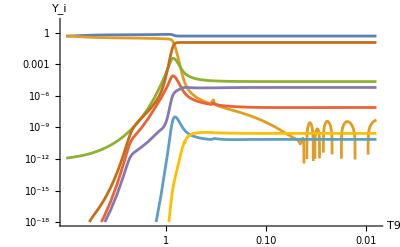
{2.69727,0.495863,4.6521,6.88816,-Graphics-}

```mathematica
BRtopipidef=0.0001;
nGL0def=5;
αGLdef=0;
accthermodef=8;(* If this increases too much there is a spike in one variable which makes it crash. Careful *)
prethermodef=8;
ηb0def=6.13744 10^-10;
τninsecsdef=878.4;
preBBNdef=8;accBBNdef=8;maxstepBBNdef=0.003;

mavaldef=10000;
taudef=10^3;
Yadef=1 0.0258; (* 0.0258 would be for a thermal axion at that time *)
Yadef=10^-6;

mavaldef=10;
taudef=0.1;
Yadef=1 0.0258; (* 0.0258 would be for a thermal axion at that time *)

resvec=Quiet[FuncNeffBBNALP[Yadef,mavaldef,taudef,BRtopipidef,nGL0def,αGLdef,accthermodef,prethermodef,ηb0def,τninsecsdef,preBBNdef,accBBNdef,maxstepBBNdef,True,5]]
```

One can tell that the thermo functions are smooth and all is good

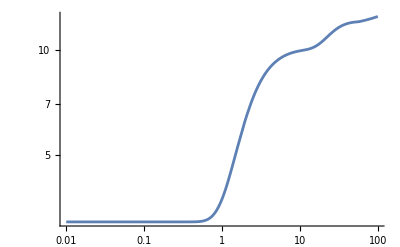

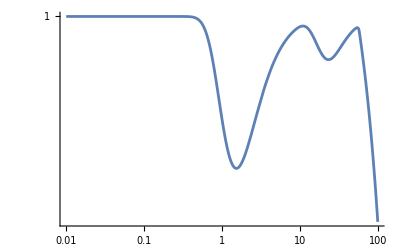

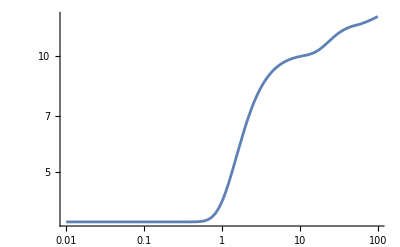

```mathematica
Print[" One can tell that the thermo functions are smooth and all is good "]
LogLogPlot[gstartab[T9],{T9,100,0.01}]
LogLogPlot[ξtab[T9],{T9,100,0.01}]
LogLogPlot[gstarStab[T9],{T9,100,0.01}]
```

```mathematica
6.112 *(0.02242/0.02237)
```

6.12566

Rat calc/thermal = 0.

initial Ya = 0.

initial Ya = 0. as input

tCPU = 2.07847 time used for solving background

tCPU = 0.313413 end interpolation from thermo

tCPU = 1.45339 end interpolation of weak rates

tCPU = 0.243297 end solution of p-n densities at high T

tCPU = 1.36851 end solution of all nucleids

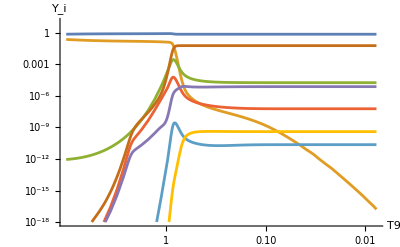
{3.03645,0.247312,2.44518,5.65549,-Graphics-}

```mathematica
BRtopipidef=0.00;
nGL0def=5;
αGLdef=0;(* I get something slightly wierd, keep at 0 *)
accthermodef=6;(* If this increases too much there is a spike in one variable which makes it crash. Careful *)
prethermodef=6;
ηb0def=6.125661153330353 10^-10;
τninsecsdef=879.4;
preBBNdef=8;accBBNdef=8;maxstepBBNdef=0.003;

mavaldef=10000;
taudef=10000;
Yadef=1 0.0258; (* 0.0258 would be for a thermal axion at that time *)
Yadef=0;

resvec=Quiet[FuncNeffBBNALP[Yadef,mavaldef,taudef,BRtopipidef,nGL0def,αGLdef,accthermodef,prethermodef,ηb0def,τninsecsdef,preBBNdef,accBBNdef,maxstepBBNdef,True]]
```

```mathematica
(* Mean values and errors from PRIMAT : Table 2 of 2011.11320 *)
Print["Precision in Yp|SM = ",NumberForm[100*Abs[1-resvec[[2]]/0.24721],2]," %"];
Print["Theory er in Yp|SM = ",NumberForm[100 0.00014/0.24721,2]," %"];
Print["Precision in DH|SM = ",NumberForm[100*Abs[1-resvec[[3]]/2.439],2]," %"];
Print["Theory er in DH|SM = ",NumberForm[100 0.037/2.439,2]," %"];
Print["Precision in 3He|SM = ",NumberForm[100*Abs[1-(N[10^5 Y3He[T9]/Yp[T9]]/.solall/.T9->Tfinv2)/1.039],2]," %"];
Print["Theory er in 3He|SM = ",NumberForm[100 0.014/1.039,2]," %"];

Print["Precision in 7Li|SM = ",NumberForm[100*Abs[1-resvec[[4]]/5.464],2]," %"];
Print["Theory er in 7Li|SM = ",NumberForm[100 0.220/5.464,2]," %"];
Print["The precision is really excellent. Good to go!!! "]
```

Precision in Yp|SM = 0.041 %

Theory er in Yp|SM = 0.057 %

Precision in DH|SM = 0.25 %

Theory er in DH|SM = 1.5 %

Precision in 3He|SM = 1.2 %

Theory er in 3He|SM = 1.3 %

Precision in 7Li|SM = 3.5 %

Theory er in 7Li|SM = 4. %

The precision is really excellent. Good to go!!!

### BBN Easy ALP [set up for parallelization]

```mathematica
(* Key routines and default parameters. This includes loading the corresponding BR and abundances for ALPs.  *)
```

#### Default technical parameters and properties

```mathematica
nGL0def=5;(* number of Gauss-Laguerre modes *)
αGLdef=0;
(* Parameters needed for the thermodynamic evolution accuracy *)
accthermodef=8;(* If this increases too much there is a spike in one variable which makes it crash. Careful *)
prethermodef=8;
(* BBN parameters, including precision and minimum timestep relevant for the nuclear abundance calculation *)
ηb0def=6.13744*10^-10;
τninsecsdef=878.4;
preBBNdef=8;accBBNdef=8;maxstepBBNdef=0.003;
```

#### Load ALP properties [BRs, abundances]

```mathematica
(*This section loads the results from the early Universe calculation telling us the Yield of the axion at T = 20 MeV as a function of mass, lifetime and reheating temperature.  : *)
(* "ALP-abundances.mx" is a Mathematica table that contains precisely that information:
Maksym fill units: m [MeV], τ [s], Treh [MeV], Yield *)

TMAX=20.;
abundances20MeV={10^3#[[1]],#[[2]],10^3#[[3]],#[[4]]}&/@Import[FileNameJoin[{NotebookDirectory[],"ALP-abundances.mx"}],"MX"];

TrehVals=abundances20MeV[[All,3]]//DeleteDuplicates
abundances20MeVint[m_,τ_,Treh_]=Interpolation[Log[{#[[1]],#[[2]],#[[3]],#[[4]]+10^-90.}&/@abundances20MeV]//Re,InterpolationOrder->1][Log[m],Log[τ],Log[Treh]]//Exp;
abundances20MeVint[m_,τ_,Treh_]=If[Treh>TMAX,Evaluate[abundances20MeVint[m,τ,Treh]],0.];
(* abundances20MeVint now is a function that can provide the abundance at T = 20 MeV. With the if statement it also works for Treh < 20 MeV and it just sets to zero the initial temperature. *)

(* "ALP-decay-Br-ratios.mx" is a Mathematica table that contains interpolation functions that contain the information on the final state multiplicity from the off-shell two-photon decays π^-[1],  K^-[2],  KL[3],  μ^-[4]:
 *)
MultiplicitiesVals[ma_]=Import[FileNameJoin[{NotebookDirectory[],"ALP-decay-Br-ratios.mx"}],"MX"];
BrToπVals[ma_]=Select[MultiplicitiesVals[10^-3. ma],#[[1]]=="π^-"&][[1]][[2]];
BrToKmVals[ma_]=Select[MultiplicitiesVals[10^-3. ma],#[[1]]=="K^-"&][[1]][[2]];
BrToKLVals[ma_]=Select[MultiplicitiesVals[10^-3. ma],#[[1]]=="K_L"&][[1]][[2]];
(*These functions give the branching ratios *)

(*"TeffALPatTfinish.mx" is a Mathematica table that given an ALP mass, lifetime, reheating temperature gives back the temperature of ALP freeze-out in MeV. This is needed to then redshift this distribution to T = 20 MeV, see Appendix C. The function aRatioFromTdecAtTmax is then used precisely for this. *)
ALPdecouplingData={10^3#[[1]],#[[2]],10^3#[[3]],10^3#[[4]],#[[5]]}&/@Import[FileNameJoin[{NotebookDirectory[],"TeffALPatTfinish.mx"}],"MX"];
TdecALP[m_,τ_,Treh_]=If[Treh>TMAX&&m>Min[ALPdecouplingData[[All,1]]],Evaluate[Interpolation[ALPdecouplingData[[All,{1,2,3,4}]]//Log,InterpolationOrder->1][Log[m],Log[τ],Log[Treh]]//Exp],Evaluate[TMAX]];
aRatioFromTdecAtTmax[m_,τ_,Treh_]=If[Treh>TMAX&&m>Min[ALPdecouplingData[[All,1]]],Evaluate[Interpolation[ALPdecouplingData[[All,{1,2,3,5}]]//Log,InterpolationOrder->1][Log[m],Log[τ],Log[Treh]]//Exp],Evaluate[1]];
```

{20.,50.,100.,1000.,10000.,100000.,200000.,1.×10^6,1.×10^9,1.×10^13,1.×10^19}

#### External routines from BBN Easy

```mathematica
(* In this section we effectively copy the key routines from BBN Easy ALP in order to build a paralellized code. Paralellization is useful as it speeds up calculations by a factor of ~8. *)

(* This is the recipy to get the Gauss-Laguerre points and weights to carry out momentum integrals.
Since we are working with a thermal state this should work very well.
 From ChatGPT *)
GaussLaguerreRule[n_,α_]:=Module[{diag,sub,J,evals,evecs,ord,x,w},diag=Table[2. k+1.+α,{k,0,n-1}];
sub=Table[Sqrt[k (k+α)],{k,1,n-1}];
(*build the symmetric tridiagonal matrix manually*)J=DiagonalMatrix[diag]+DiagonalMatrix[sub,1]+DiagonalMatrix[sub,-1];
{evals,evecs}=Eigensystem[J];
ord=Ordering[evals];
x=evals[[ord]];
w=Gamma[α+1.] (evecs[[ord,1]]^2);
{x,w}];
(*ALP collision terms*)
(* The first term is a <-> γ γ and the second e γ <-> e a. They are the versions from Eqs. 3.3 and 3.4 of 1110.2895 *)
Cterm[ma_,p_,T_,τa_,mγ_,DecayOnly_,StimEmission_]:=1/τa(ma^2-4 mγ^2)/ma^2 Piecewise[{{1,ma>=2mγ}},0] ma/(√(ma^2+p^2))(1+If[StimEmission,(2 T)/p Log[(1-ⅇ^((-p-√(ma^2+p^2))/(2 T)))/(1-ⅇ^((p-√(ma^2+p^2))/(2 T)))],0])+If[!DecayOnly,1/137*1/16(64π)/(ma^3 τa) 4nFDM[T,0,me]Log[1+((4 √(ma^2+p^2)(me+3T))^2)/(mγ^2(me^2+(me+3T)^2))],0.];
Ctermy[ma_,y_,T_,a_,m0_,τa_,mγ_,DecayOnly_,StimEmission_]:=Cterm[ma,m0 y/a,T,τa,mγ,DecayOnly,StimEmission];
(* Photon plasma mass, from Eq. 12 in hep-ph/9702324 summed over just electrons
Here hofmu is the Bessel function expansion for it.
*)
hofmu[τ_]:=Sum[((-1)^n τ BesselK[1,(1+n) τ])/(1+n),{n,0,30}];

mγfunc[T_]:=(8/(137 π)T^2 hofmu[me/T])^(1/2);
(* Bose-Einstein axion equilibrium distribution function *)
faeq[ma_,y_,T_,a_,m0_]:=1/(-1+Exp[(√(ma^2+(m0 y/a)^2))/T]);
ρϕfunc0[ma_,yvec_,a_,m0_,wGL_,xGL_,αGL_,nGL_]:=1/(2 π^2)(m0/a)^4 Sum[wGL[[i]]*xGL[[i]]^(2-αGL)*√(xGL[[i]]^2+((ma a)/m0)^2)*yvec[[i]],{i,2,nGL}];
(* ϕ number density *)
nϕfunc0[ma_,yvec_,a_,m0_,wGL_,xGL_,αGL_,nGL_]:=1/(2 π^2)(m0/a)^3 Sum[wGL[[i]]*xGL[[i]]^(2-αGL)*yvec[[i]],{i,2,nGL}];
(* ϕ pressure *)
pϕfunc0[ma_,yvec_,a_,m0_,wGL_,xGL_,αGL_,nGL_]:=1/(2 π^2)(m0/a)^4 Sum[wGL[[i]]*xGL[[i]]^(4-αGL)/(3 √(xGL[[i]]^2+((ma a)/m0)^2))*yvec[[i]],{i,2,nGL}];
dρϕdt0[ma_,yvec_,a_,m0_,aprime_,yvecprime_,wGL_,xGL_,αGL_,nGL_]:=1/(2 π^2)Sum[wGL[[i]]*xGL[[i]]^(2-αGL)(m0^2 (-3 a^2 aprime ma^2 yvec[[i]]-4 aprime m0^2 xGL[[i]]^2 yvec[[i]]+a^3 ma^2 yvecprime[[i]]+a m0^2 xGL[[i]]^2 yvecprime[[i]]))/(a^5 √((a^2 ma^2)/m0^2+xGL[[i]]^2)),{i,2,nGL}];
sSM[Tγ_,Tν_]=((2(ρBE[Tγ,0]+pBE[Tγ,0])+4 (ρFDM[Tγ,0,me]+pFDM[Tγ,0,me]))/Tγ+4/3* 6 ρFD[Tν,0]/Tν);
collSource[feq_,f_,DecayOnly_]:=If[DecayOnly,-f,feq-f];
Qofaxion0[ma_,yvec_,T_,a_,m0_,τa_,wGL_,xGL_,αGL_,nGL_,DecayOnly_,StimEmission_]:=Sum[1/(2 π^2)(m0/a)^4 wGL[[i]]*xGL[[i]]^(2-αGL)*√(xGL[[i]]^2+((ma a)/m0)^2) Ctermy[ma,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0,τa,mγfunc[yvec[[nGL+2]]],DecayOnly,StimEmission]*(*(faeq[ma,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0]-yvec[[i]])*)collSource[faeq[ma,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0],yvec[[i]],DecayOnly] ,{i,2,nGL}];
Hoftsim[Tγ_]:=(√((8π)/3 π^2/30) √10.75 Tγ^2/Mpl);
t0Tmax[Tmax_]:=1/(2Hoftsim[Tmax] FacMeVtos1);
MeVto109K=11.60451812;(* Key conversion factor to put everything at 10^9 K *)
Δmval=1.29333;(* This is mn-mp in MeV *)
(* This loads the radiative corrections within the SM. It should be a good approx just to take them BSM. *)
Corrpn=Interpolation[Import["WeakRates/Gamma_pn_Corr.dat",HeaderLines->1][[All,{1,2}]],InterpolationOrder->1];
Corrnp=Interpolation[Import["WeakRates/Gamma_np_Corr.dat",HeaderLines->1][[All,{1,2}]],InterpolationOrder->1];
nb=η10func 10^-10*2 Zeta[3]/π^2 T^3;
ηBfunc= 10^-10 η10func;
(* Born rate integral taken using the formulae from Dicus et al. '82 *)
Rate[TνinMeV_,TγinMeV_,q_]:=With[{zγ=me/TγinMeV, zν= me/TνinMeV},(NIntegrate[(((ϵ-q)^2(ϵ^2-1)^(1/2)ϵ)/((1+Exp[-ϵ zγ])(1+Exp[(ϵ-q)zν]))+((ϵ+q)^2(ϵ^2-1)^(1/2)ϵ)/((1+Exp[ϵ zγ])(1+Exp[-(ϵ+q)zν]))),{ϵ,1,Infinity}])];
NormFactor=Rate[10^-6,10^-6,Δmval/me];
```

### Main routine

```mathematica
(* Paralellized routine. At the end, there is the key function: FuncNeffBBNALPfinal. That's the one we actually use as it runs with standard settings. *)
```

#### FuncNeffBBNALPparallel

```mathematica
FuncNeffBBNALPparallel[DecayOnly_,StimEmission_,Yaval_,maval_,τaval_,Tdec_,aRatioFromTdec_,BRtopipi_:0,nGL0_:5,αGL_:0,accthermo_:8,prethermo_:8,ηb0_:6.13744*10^-10,τninsecs_:878.4,preBBN_:8,accBBN_:8,maxstepBBN_:0.003,printflag_:False,Tmax_:20]:=Module[{Tini=4 MeVto109K,Tfin=9,Tmin=0.0005,t0=t0Tmax[Tmax],KK=(NormFactor (τninsecs s))^-1,tcut=500,YDini=0,Tiniv2=10,tmax1,tvecint,tmax,xGL,wGL,nGL,m0val,supfactor,vecf0,Tγcut,ρϕfunc,nϕfunc,pϕfunc,dρϕdt,ρtot,ptot,Hubble,RHSec,dρtotdt,Qofaxion,dTγdt,dTνdt,rhs,solu,Tγoftfunc,Tνoftfunc,aoftfunc,gstartab,ξtab,gstarStab,ρXtab,nXtab,f,ff,fff,λnptabaux,λnptab,λpntabaux,λpntab,λnp,λpn,npiplus,npiminus,λnppionRate,λpnpionRate,npipluspost,npiminuspost,λnppionRatepost,λpnpionRatepost,Hubfunc,ξfunc,ηbtab,δYnδtweak,δYDδtnp,δY3HeδtDD3Hen,δYTδtDDTp,λpi4HeTn,λpi4HeD2n,λpi4Hep3n,δY4Heδt,solpn,η10bini,rhsvecpn,δYpδt,δYnδt,δYDδt,δYTδt,δY3Heδt,δY7Liδt,δY7Beδt,δYTδt3HenTp,δ3HeδtDp3Heγ,δY4Heδt3HeD4Hep,δY4HeδtTD4Hen,δY7Liδt4HeT7Liγ,δY4Heδt7Lip4He4He,δY7Beδt4He3He7Be,δY7Beδt7Ben7Lip,δY4HeδtTp4Heγ,
rhsvecall,Tfinv2,Ypini,Ynini,solall,plotnucleids,yEq,nEqTa},
(*Max time of the integration*)
tmax1=1/(2Hoftsim[Tmin] FacMeVtos1);
tmax=Max[tmax1,10*τaval];
(* Yaval = dimensionless yield. maval = mass in MeV, τaval = lifetime in seconds, BRtopipi = BR to pions. *)
(* nGL, Number of Gauss-Laguerre nodes. 10 gives very good results both for phi but also for associated quantities. *)
(* αGL, is the power specified and one could choose 2 or 3 (and modify formulas accordingly to find best convergence for n or rho )*)
(* accthermo and prethermo are the accuracy and precision goals of the solver. with 6 one gets quite accurate results. It is recommended to use the 6 as going to higher accuracy may lead to some instabilities in derived parameters. With precision 8 one can see that the continuity equation is fulfilled with < 10^-5 precision. Which is really really good.
*)
(* For BBN, the setting:
preBBN=8;accBBN=8;maxstepBBN=0.003; is the default. 
Requiring higher precision may brake the code if one is having too crazy cosmologies of hadron injections.
*)
(* Tmax is the starting temperature, typically set to be 20 MeV, but can be chosen smaller. *)
{xGL,wGL}=GaussLaguerreRule[nGL0,αGL];
xGL=Join[{10^-5},xGL];(*Here we add a fake low momentum bin so that it does not complain. Somehow that bin grows a lot (possibly Bose condensation, see hep-ph/9409202)
By integrating from 2 to nGL we get rid of this in all integrals. *)
wGL=Join[{0},wGL];
wGL=Exp[xGL]*wGL;(* This is done to automatically add the e^x weight needed in the calculations! *)
nGL=nGL0+1;
(* Here the αGL power is added in order to re-define the weightings *)
ρϕfunc[ma_,yvec_,a_,m0_]:=ρϕfunc0[ma,yvec,a,m0,wGL,xGL,αGL,nGL];
nϕfunc[ma_,yvec_,a_,m0_]:=nϕfunc0[ma,yvec,a,m0,wGL,xGL,αGL,nGL];
pϕfunc[ma_,yvec_,a_,m0_]:=pϕfunc0[ma,yvec,a,m0,wGL,xGL,αGL,nGL];
(*
This expression comes from:
D[(m0/a[x])^4 √(xx^2+((ma a[x])/m0)^2)*y[x],x]/.{y'[x]->yvecprime,y[x]->yvec,a[x]->a,a'[x]->aprime}//Simplify
*)
dρϕdt[ma_,yvec_,a_,m0_,aprime_,yvecprime_]:=dρϕdt0[ma,yvec,a,m0,aprime,yvecprime,wGL,xGL,αGL,nGL];
(* Includes neutrinos, e+e-, photons and the axion *)
ρtot[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=(2ρBE[Tγ,0]+4 ρFDM[Tγ,0,me]+6ρFD[Tν,0]+ρϕfunc[ma,yvec,a,m0]);
ptot[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=(2pBE[Tγ,0]+4 pFDM[Tγ,0,me]+6pFD[Tν,0]+pϕfunc[ma,yvec,a,m0]);
Hubble[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=((ρtot[Tγ,Tν,ma,yvec,a,m0]) (8 π)/(3 (Mpl)^2))^(1/2)FacMeVtos1;
(* -3H(ρtot+ptot) *)
RHSec[Tγ_,Tν_,ma_,yvec_,a_,m0_]:=-3 Hubble[Tγ,Tν,ma,yvec,a,m0](ρtot[Tγ,Tν,ma,yvec,a,m0]+ ptot[Tγ,Tν,ma,yvec,a,m0]);
(* dρtot/dt *)
dρtotdt[ma_,yvec_,a_,m0_,aprime_,yvecprime_,T_,Tp_,Tnu_,Tnup_]:=dρϕdt[ma,yvec,a,m0,aprime,yvecprime]+(2dρBEdT[T,0]Tp+4 dρdTFDM[T,0,me]Tp+6dρFDdT[Tnu,0]Tnup);
(* Axion energy transfer rate *)
Qofaxion[ma_,yvec_,T_,a_,m0_,τa_]:=Qofaxion0[ma,yvec,T,a,m0,τa,wGL,xGL,αGL,nGL,DecayOnly,StimEmission];
(* Equation 2.14 of 1812.05605 *)
dTγdt[Tγ_,Tν_,ma_,yvec_,a_,m0_,τa_]:=-1/(2 (2 π^2 Tγ^3)/15+4dρdTFDM[Tγ,0,me])( Hubble[Tγ,Tν,ma,yvec,a,m0] ( 4*2 ρBE[Tγ,0]+3*4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me]))+Qofaxion[ma,yvec,Tγ,a,m0,τa] + ΔρSMνe[Tγ,Tν,Tν,0,0]+2 ΔρSMνμ[Tγ,Tν,Tν,0,0]);
(* Equations 2.9 of 1812.05605 *)
dTνdt[Tγ_,Tν_,ma_,yvec_,a_,m0_,τa_]:=-Hubble[Tγ,Tν,ma,yvec,a,m0] Tν +1/3 (ΔρSMνe[Tγ,Tν,Tν,0,0]+2ΔρSMνμ[Tγ,Tν,Tν,0,0])/(2dρFDdT[Tν,0]);
(*
m0val=Tmax; (* MeV. This is done because we use the scale factor a = 1 at the starting point. This is needed to have the correct normalization of the axion number/energy density.*)
(*contents:(f[nGL dims],nGL+1[a],nGL+2[Tγ],nGL+3[Tν])*)
supfactor=Yaval sSM[Tmax,Tmax]/nBE[Tmax,0];
vecf0=Join[Table[faeq[0,xGL[[i]],Tmax,1,m0val],{i,1,nGL}],{1},{Tmax},{Tmax}];
vecf0=Join[Table[supfactor faeq[0,xGL[[i]],Tmax,1,m0val],{i,1,nGL}],{1},{Tmax},{Tmax}];
vecf0[[1]]=0;
*)
m0val=Tmax;  (*a(t0)=1 normalization,as before*)
(*---Build equilibrium shape at TaStart WITH MASS maval---*)
yEq=Table[faeq[maval,xGL[[i]],Tdec,1/aRatioFromTdec,m0val],{i,1,nGL}];
(*Equilibrium number density at TaStart (same quadrature as elsewhere)*)
nEqTa=nϕfunc[maval,yEq,1,m0val];
(*Fugacity to enforce Y=n/s_SM at Tγ=Tmax,Tν=Tmax*)
supfactor=Yaval*sSM[Tmax,Tmax]/nEqTa;
(*Initial state:use the cooler ALP kinetic temperature (TaStart),not Tγ,and scale by supfactor to set the number density.*)
vecf0=Join[supfactor*yEq,{1},{Tmax},{Tmax}];
vecf0[[1]]=0;  (*keep your low-y smoothing*)
If[printflag==True,
Print["Rat calc/thermal = ",nϕfunc[maval,vecf0,1,m0val]/nBE[Tmax,0]];
Print["initial Ya = ",NumberForm[nϕfunc[maval,vecf0,1,m0val]/sSM[Tmax,Tmax],2]];
Print["initial Ya = ",NumberForm[N[Yaval],2]," as input"];
];
rhs[t_,yvec_]:=Module[{row},(*contents: (f[nGL dims], nGL+1 [a], nGL+2 [Tγ], nGL+3 [Tν]) *)row=Table[ Ctermy[maval,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0val,τaval,mγfunc[yvec[[nGL+2]]],DecayOnly,StimEmission]*collSource[faeq[maval,xGL[[i]],yvec[[nGL+2]],yvec[[nGL+1]],m0val],yvec[[i]],DecayOnly],{i,1,nGL}];
Join[row,{yvec[[nGL+1]](Hubble[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val])},{dTγdt[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val,τaval]},{dTνdt[yvec[[nGL+2]],yvec[[nGL+3]],maval,yvec,yvec[[nGL+1]],m0val,τaval]}]];
solu=Quiet[NDSolveValue[{f'[t]==rhs[t,f[t]],f[t0]==vecf0},f,
{t,t0,tmax},AccuracyGoal->accthermo,PrecisionGoal->prethermo,Method->{"BDF"}]];
Tγoftfunc[t1_]:=solu[t1][[nGL+2]];
Tνoftfunc[t1_]:=solu[t1][[nGL+3]];
aoftfunc[t1_]:=solu[t1][[nGL+1]];
(* We will interpolate over the same points of the grid from the solution *)
tvecint=Flatten[solu["Grid"]];
gstartab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],1/FacMeVtos1^2((90 Mpl^2 Quiet[Hubble[solu[tvecint[[i]]][[nGL+2]],solu[tvecint[[i]]][[nGL+3]],maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val]^2])/(8 π^3 Tγoftfunc[tvecint[[i]]]^4))},{i,1,Length[tvecint]}],InterpolationOrder->1];
ξtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],-solu'[tvecint[[i]]][[nGL+2]]/Quiet[Hubble[solu[tvecint[[i]]][[nGL+2]],solu[tvecint[[i]]][[nGL+3]],maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val]* Tγoftfunc[tvecint[[i]]]]},{i,1,Length[tvecint]}],InterpolationOrder->1];(* For this function we choose interpolation order 1 because since it involves derivatives, Interpolation Order -> 3 can make it a bit wierd otherwise *)
gstarStab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],gstartab[MeVto109K Tγoftfunc[t0]](Tγoftfunc[t0]/Tγoftfunc[tvecint[[i]]])^3 (aoftfunc[t0]/aoftfunc[tvecint[[i]]])^3 },{i,1,Length[tvecint]}],InterpolationOrder->1];
ρXtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],ρϕfunc[maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val] },{i,1,Length[tvecint]}],InterpolationOrder->1];
nXtab=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],nϕfunc[maval,solu[tvecint[[i]]],solu[tvecint[[i]]][[nGL+1]],m0val] },{i,1,Length[tvecint]}],InterpolationOrder->1];
(* Same vector as before, but now just evaluate the integrals at t < 500 s. After they are either 0 (p->n), or 1, free-lifetime. *)
Tγcut=MeVto109K Tγoftfunc[500];
tvecint=Select[Flatten[solu["Grid"]],#<tcut&];
λnptabaux=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],Rate[Tνoftfunc[tvecint[[i]]],Tγoftfunc[tvecint[[i]]],Δmval/me] },{i,1,Length[tvecint]}],InterpolationOrder->3];
λnptab[T_]:=Piecewise[{{λnptabaux[T],T>Tγcut}},1];
λpntabaux=Interpolation[Table[{MeVto109K Tγoftfunc[tvecint[[i]]],Rate[Tνoftfunc[tvecint[[i]]],Tγoftfunc[tvecint[[i]]],-Δmval/me] },{i,1,Length[tvecint]}],InterpolationOrder->3];

λpntab[T_]:=Piecewise[{{λpntabaux[T],T>Tγcut}},0];
(* With the radiative corrections *)
λnp=KK λnptab[T9]*Corrnp[T9]; 
λpn=KK λpntab[T9]*Corrpn[T9];
(* Including now the effect from meson driven interactions: *)
(* MDI *)
npiplus=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminus=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp) );
λnppionRate=nXtab[T9] MeV^3 npiplus σvnppi[T9];

λpnpionRate=nXtab[T9] MeV^3 npiminus σvpnpi[T9];

(* These formulas are used for the calculation once 4He can start to form (although the results will not actually change appreciably) *)
npipluspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminuspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp+(σvpi4HeTn[T9]+σvpi4HeD2n[T9]+σvpi4Hep3n[T9])nb Y4He) );
λnppionRatepost=nXtab[T9] MeV^3 npipluspost σvnppi[T9];

λpnpionRatepost=nXtab[T9] MeV^3 npiminuspost σvpnpi[T9];
(* Define Key Functions: *)
Hubfunc=1.66 √gstartab[T9] T^2/Mpla/.Mpla->1.22 10^19 10^3 MeV;
ξfunc =ξtab[T9];
ηbtab[T9_]:=ηb0 *gstarStab[T9]/gstarStab[MeVto109K Tγoftfunc[tmax]];
(* Relevant nucleid abundances: *)
δYnδtweak=Yp( λpn+λpnpionRate)-Yn (λnp+λnppionRate) ;(* n <-> p conversion *)
δYDδtnp=nb( σvpntoDγ Yn Yp -σvpntoDγrev YD (1/ηBfunc));(* n + p  <-> D + γ conversion *)

δY3HeδtDD3Hen=nb(1/2 σvDDto3Hen YD YD-σvDDto3Henrev Y3He Yn);(* D + D  <-> 3He + n conversion *)
δYTδtDDTp=nb(1/2 σvDDtoTp YD YD -σvDDtoTprev YT Yp);
(* D + D  <-> T + p conversion *)
δYTδt3HenTp=nb(σv3HentoTp Y3He Yn -σv3HentoTprev YT Yp);
(* 3He + n  <-> T + p conversion *)
δ3HeδtDp3Heγ=nb(σvDpto3Heγ YD Yp -σvDpto3Heγrev Y3He (1/ηBfunc));
(* D + p  <-> 3He + γ conversion *)
δY4Heδt3HeD4Hep=nb(σv3HeDto4Hep Y3He YD -σv3HeDto4Heprev Y4He Yp); (* 3He + D  <-> 4He + p conversion *)
δY4HeδtTD4Hen=nb(σvTDto4Hen YT YD -σvTDto4Henrev Y4He Yn); 
 (* T + D  <-> 4He + n conversion *)
δY7Liδt4HeT7Liγ=nb(σvT4Heto7Liγ Y4He YT -σvT4Heto7Liγrev Y7Li(1/ηBfunc)); (* 4He + T  <-> 7Li + γ conversion *)

δY4Heδt7Lip4He4He=nb(σv7Lipto4He4He Y7Li Yp -σv7Lipto4He4Herev 1/2 Y4He Y4He); (* 7Li + p <-> 4He + 4He  conversion *)

δY7Beδt4He3He7Be=nb(σv4He3Heto7Beγ Y4He Y3He -σv4He3Heto7Beγrev Y7Be (1/ηBfunc)); (* 4He + 3He <-> 7Be + γ  conversion *)

δY7Beδt7Ben7Lip=-nb(σv7Bento7Lip Y7Be Yn -σv7Bento7Liprev Y7Li Yp); (* 7Be + n <-> 7Li + p  conversion *)

δY4HeδtTp4Heγ=nb(σvTpto4Heγ YT Yp -σvTpto4Heγrev Y4He (1/ηBfunc) ); (* T + p  <-> 4He + γ conversion *)

δYpδt=-δYnδtweak-δYDδtnp+δYTδtDDTp+δY4Heδt3HeD4Hep-δY4Heδt7Lip4He4He+δYTδt3HenTp-δ3HeδtDp3Heγ-δY7Beδt7Ben7Lip-δY4HeδtTp4Heγ;
δYnδt=δYnδtweak-δYDδtnp+δY3HeδtDD3Hen+δY4HeδtTD4Hen-δYTδt3HenTp+δY7Beδt7Ben7Lip;
δYDδt=δYDδtnp-2δYTδtDDTp-2δY3HeδtDD3Hen-δY4HeδtTD4Hen-δY4Heδt3HeD4Hep-δ3HeδtDp3Heγ;
δYTδt=δYTδtDDTp-δY7Liδt4HeT7Liγ-δY4HeδtTD4Hen+δYTδt3HenTp-δY4HeδtTp4Heγ;
δY3Heδt=δY3HeδtDD3Hen-δY4Heδt3HeD4Hep-δY7Beδt4He3He7Be-δYTδt3HenTp+δ3HeδtDp3Heγ;
δY4Heδt=δY4HeδtTD4Hen+δY4Heδt3HeD4Hep-δY7Liδt4HeT7Liγ+2δY4Heδt7Lip4He4He-δY7Beδt4He3He7Be+δY4HeδtTp4Heγ;
δY7Liδt=δY7Liδt4HeT7Liγ-δY4Heδt7Lip4He4He-δY7Beδt7Ben7Lip;
δY7Beδt=δY7Beδt4He3He7Be+δY7Beδt7Ben7Lip;
(*δY7Beδt=-(δYpδt+δYnδt+2δYDδt+3δYTδt+3δY3Heδt+4δY4Heδt+7δY7Liδt)/7;*)
(* Solve for the neutron abundance! *)
rhsvecpn=Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){-δYnδtweak,δYnδtweak}]/.{s->1/(6.582119×10^-16  10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],η10func->η10func[T9],T->T9 10^9 Kel,MeV-> 10^6 11604.51812 Kel}/.Kel->1;
ff[T9_]={η10func[T9],Yp[T9],Yn[T9]};

(* Start at 4 MeV. Then the interactions are still very fast and some numerical instabilities from the thermo solver should be irrelevant. *)
η10bini=ηbtab[T9]/10^-10/.T9->Tini;
solpn=NDSolve[{ff'[T9]==rhsvecpn,
Yp[Tini]==0.5,Yn[Tini]==0.5,η10func[Tini]==η10bini},
{Yp,Yn,η10func},
{T9,Tini,Tfin},
AccuracyGoal->accBBN,PrecisionGoal->preBBN,
MaxSteps->10^8,MaxStepSize->maxstepBBN,Method->"BDF"]//First;
(*MaxStepSize->0.001 which is a factor of 1 smaller than before, and also precision and acc goals are 10 now. *)
(* MDI, now that the basic equation for the neutron density has been solved we go and consider the case of the destruction of 4He as well *)
npipluspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvnppi[T9]nb Yn) );
npiminuspost=( (1/(τaval s) BRtopipi)/(1/τpi+σvpnpi[T9]nb Yp+(σvpi4HeTn[T9]+σvpi4HeD2n[T9]+σvpi4Hep3n[T9])nb Y4He) );
λpi4HeTn=nXtab[T9] MeV^3 npiminuspost σvpi4HeTn[T9];
λpi4HeD2n=nXtab[T9] MeV^3 npiminuspost σvpi4HeD2n[T9];
λpi4Hep3n=nXtab[T9] MeV^3 npiminuspost σvpi4Hep3n[T9];

δY4Heδt=δY4Heδt-(λpi4HeTn+λpi4HeD2n+λpi4Hep3n)Y4He;
δYTδt=δYTδt+(λpi4HeTn)Y4He;
δYDδt=δYDδt+(λpi4HeD2n)Y4He;
δYpδt=δYpδt+(λpi4Hep3n)Y4He;
δYnδt=δYnδt+(λpi4HeTn)Y4He+2(λpi4HeD2n)Y4He+3(λpi4Hep3n)Y4He;

(*SOLVE FOR ALL nucleids *)
(*
rhsvecall=Simplify[Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){δYpδt,δYnδt,δYDδt,δYTδt,δY3Heδt,δY4Heδt,δY7Liδt,δY7Beδt}]/.cm->10^-2 m/.{s->1/(6.582119×10^-16  10^-6 MeV),m->1/(1.97327×10^-7 10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],YD->YD[T9],YT->YT[T9],Y3He->Y3He[T9],Y4He->Y4He[T9],Y7Li->Y7Li[T9],Y7Be->Y7Be[T9],T->T9 10^9 Kel,MeV-> 10^6 11604.51812 Kel,η10func->η10func[T9]}]/.Kel->1;
*)
rhsvecall=(Join[{3 η10func/T9(1/ξfunc-1)},-1/(Hubfunc T9 ξfunc){δYpδt,δYnδt,δYDδt,δYTδt,δY3Heδt,δY4Heδt,δY7Liδt,δY7Beδt}]/.cm->10^-2 m/.{s->1/(6.582119×10^-16*10^-6 MeV),m->1/(1.97327×10^-7*10^-6 MeV)}/.{Yp->Yp[T9],Yn->Yn[T9],YD->YD[T9],YT->YT[T9],Y3He->Y3He[T9],Y4He->Y4He[T9],Y7Li->Y7Li[T9],Y7Be->Y7Be[T9],T->T9 10^9 Kel,MeV-> 10^6*11604.51812 Kel,η10func->η10func[T9]})/.Kel->1;
(* Here Kel->1 because even though the result is dimensionless it remains in some squares etc. *)
fff[T9_]={η10func[T9],Yp[T9],Yn[T9],YD[T9],YT[T9],Y3He[T9],Y4He[T9],Y7Li[T9],Y7Be[T9]};
Tfinv2=MeVto109K Tγoftfunc[tmax];
Ypini=Yp[T9]/.solpn/.T9->Tiniv2;
Ynini=Yn[T9]/.solpn/.T9->Tiniv2;
η10bini=ηbtab[T9]/10^-10/.T9->Tiniv2;
(* Warning: Set to Quiet, but it complains because the WorkingPrecision is high. This is however important because otherwise the system will get crazy with small numbers from tiny inverse reaction rates. DO NOT reduce the AccuracyGoal and PrecisionGoal. This is the minimum to get sensible stuff. Also WorkingPrecision->15 is needed.  *)

solall=Quiet[Check[First[NDSolve[Rationalize[{fff'[T9]==rhsvecall,
Yp[Tiniv2]==Ypini,Yn[Tiniv2]==Ynini,YD[Tiniv2]==YDini,YT[Tiniv2]==0,Y3He[Tiniv2]==0,Y4He[Tiniv2]==0,Y7Li[Tiniv2]==0,Y7Be[Tiniv2]==0,η10func[Tiniv2]==η10bini},0],
{Yp,Yn,YD,YT,Y3He,Y4He,Y7Li,Y7Be,η10func},
{T9,Tiniv2,Tfinv2},
AccuracyGoal->accBBN,PrecisionGoal->preBBN,
MaxSteps->10^8,MaxStepSize->maxstepBBN,Method->"BDF",WorkingPrecision->15]],(*returned only if ndsz occurs:*)Missing["NDSolveFailed","ndsz"],{NDSolve::ndsz}],{NDSolve::ndsz}];

(* Default: AccuracyGoal->8,PrecisionGoal->7,
MaxSteps->10^8,MaxStepSize->0.003, *)

If[solall===Missing["NDSolveFailed","ndsz"],

Return[{99,99,(11/4)^(4/3)6/2(Tνoftfunc[tmax]/Tγoftfunc[tmax])^4,99,99}];
,

plotnucleids=
LogLogPlot[{Yp[T9]/.solall,Yn[T9]/.solall,YD[T9]/.solall,YT[T9]/.solall,Y3He[T9]/.solall,Y4He[T9]/.solall,Y7Li[T9]/.solall,Y7Be[T9]/.solall},{T9,Tiniv2,Tfinv2},PlotRange->{10^-18,10},ScalingFunctions->{"Reverse",Automatic},WorkingPrecision->6,AxesLabel->{"T9","Y_i"}];

(* One can play a bit more with MaxStepSize, but it doesn't give you much. These settings seem pretty stable. It is never a bad idea to increas AccuracyGoal a bit. *)


Return[{(11/4)^(4/3)6/2(Tνoftfunc[tmax]/Tγoftfunc[tmax])^4,Re[N[4Y4He[T9],3]]/.solall/.T9->Tfinv2,Re[N[10^5 YD[T9]/Yp[T9],3]]/.solall/.T9->Tfinv2,Re[N[10^10(Y7Li[T9]+Y7Be[T9])/Yp[T9],3]]/.solall/.T9->Tfinv2,plotnucleids}];

];
]
```

#### FuncNeffBBNALPfinal

```mathematica
FuncNeffBBNALPfinal[mALP_,τALP_,Treh_,DecayOnly_,StimEmission_]:=Block[{BrALPtoππ=BrToπVals[mALP],YaIni=abundances20MeVint[mALP,τALP,Treh],Tdec=TdecALP[mALP,τALP,Treh],aRatioFromTdec=aRatioFromTdecAtTmax[mALP,τALP,Treh]},
Join[{mALP,τALP,Treh},FuncNeffBBNALPparallel[DecayOnly,StimEmission,YaIni,mALP,τALP,Tdec,aRatioFromTdec,BrALPtoππ,nGL0def,αGLdef,accthermodef,prethermodef,ηb0def,τninsecsdef,preBBNdef,accBBNdef,maxstepBBNdef,False,TMAX]]
]
```

```mathematica
{#,abundances20MeVint[#,10^3.,10^19.]}&/@{10.,100,1000.,10000.}
```

{{10.,0.00242531},{100,0.0023669},{1000.,0.00236694},{10000.,0.00236682}}

## Tests and examples

```mathematica
(* Here we show how the code can be used and highlight some tests. 
1) takes ~60 seconds to run
   2) takes ~4 mins *)
```

#### 1) Parallelization efficiency example

```mathematica
(* Example with axion masses 10-300 MeV, with a 1 second lifetime, and TRH = 5-60 MeV *)
triples=Tuples[{{10.,20.,30.,50.,100.,200.,250.,300.},{1.},{5.,10.,50.,60.}}];
triples//Length
ffff=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],False,True][[1;;7]],60,{-89,-89,-89,-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];//AbsoluteTiming
```

32

{56.0084,Null}

```mathematica
(* This example shows that for this example one single evaluation takes ~0.5 seconds in our laptop which is quite fast. 
Note that TimeConstrained to 60 seconds is used as some cases with huge BR into hadrons or abundances may stress test our code. If it fails to evaluate it gives -89 to signal an error.
*)
```

#### 2) Some examples: decays only vs decays + Primakoff

```mathematica
(* In this section we show that is the difference in the results when considering decays and inverse decays with or without the Primakoff effect. One clearly see that for large masses or long lifetimes the role of Primakoff at T < 20 MeV is irrelevant but for short lifetimes and light the masses not taking into account Primakoff has important implications. *)
```

τ = 0.1 s

```mathematica
mtest=1.;
τtest=0.1;
TrehTest=10^5.;
triples=Tuples[{{1.,2.,3.,4.,5.,7.5,10.,15.,20.,25.,30.,35.,40.,45.,50.,60.,70.,80.,90.,100.,125.,150.,175.,200.,225.,250.,275.,300.},{τtest},{TrehTest}}];
dat1=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],False,True][[1;;7]],60,{-89,-89,-89,-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];
dat2=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],True,True][[1;;7]],60,{-89,-89,-89,-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];
```

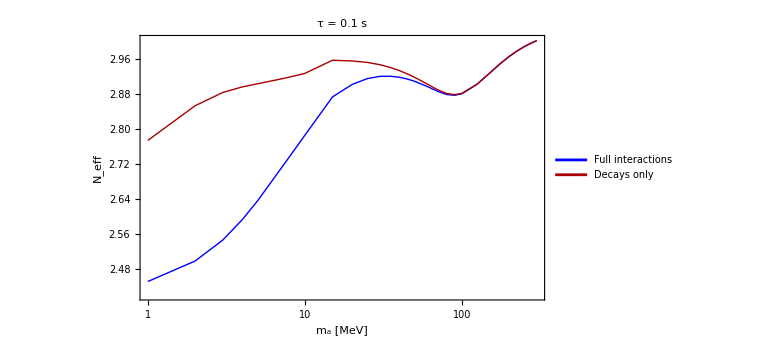

```mathematica
ListLogLinearPlot[{dat1[[All,{1,4}]],dat2[[All,{1,4}]]},Joined->True,Frame->True,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"m_a [MeV]","N_eff"},PlotStyle->({Thick,#}&/@{Blue,Darker@Red}),PlotLegends->Placed[Style[Row[{#}],20,Black]&/@{"Full interactions","Decays only"}, {0.8,0.1}],ImageSize->Large,PlotRange->{MinMax[dat2[[All,1]]],All},PlotLabel->"τ = 0.1 s"]
```

τ = 10^3 s

```mathematica
τtest=10^3;
TrehTest=10^5.;
triples=Tuples[{{1.,2.,3.,4.,5.,7.5,10.,15.,20.,25.,30.,35.,40.,45.,50.,60.,70.,80.,90.,100.,125.,150.,175.,200.,225.,250.,275.,300.},{τtest},{TrehTest}}];
dat1=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],False,True][[1;;7]],60,{-89,-89,-89,-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];
dat2=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],True,True][[1;;7]],60,{-89,-89,-89,-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];
```

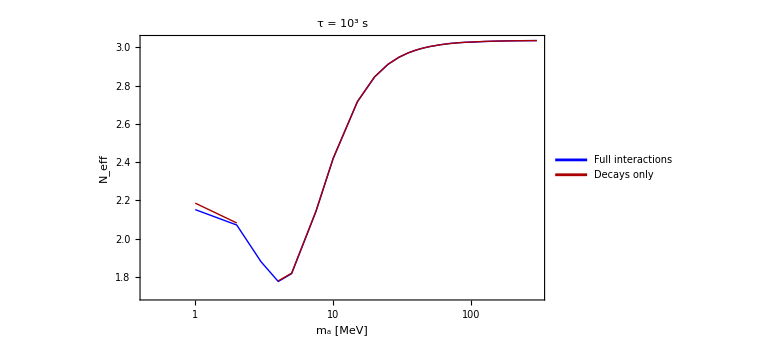

```mathematica
ListLogLinearPlot[{dat1[[All,{1,4}]],dat2[[All,{1,4}]]},Joined->True,Frame->True,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"m_a [MeV]","N_eff"},PlotStyle->({Thick,#}&/@{Blue,Darker@Red}),PlotLegends->Placed[Style[Row[{#}],20,Black]&/@{"Full interactions","Decays only"}, {0.8,0.1}],ImageSize->Large,PlotRange->{MinMax[dat2[[All,1]]],All},PlotLabel->"τ = 10^3 s"]
```

## Parameter space exploration

```mathematica
(* Here we show how the entire parameter space may be explored. It takes ~10 mins to run and the grid can be made significantly denser to get more detailed results if one wishes. *)
```

### Parallel run

#### Grid

```mathematica
(* Build a grid for ALP lifetimes [s], masses [MeV], and reheating temperatures [MeV] *)
τXmin=10^-2;τXmax=10^4;numτX=2;
tauvec = Table[N[10^i],{i,Log10[τXmin],Log10[τXmax],(Log10[τXmax]-Log10[τXmin])/numτX}]//N//Developer`ToPackedArray
(*This is actually mass in MeV*)
mXmin=10^-2;mXmax=10^3;nummX=5;
RhoXvec = Table[N[10^i],{i,Log10[mXmin],Log10[mXmax],(Log10[mXmax]-Log10[mXmin])/(nummX-1)}]//N//Developer`ToPackedArray
TrehValsFin={(*5.,10.,20.,1000.,100000.,200000.,10^6.,10^9.,10^13.,10^19.*)50.,100.,10^4.,10^6.}//Sort//N//Developer`ToPackedArray;
triples=Tuples[{RhoXvec,tauvec,TrehValsFin}]//N//Developer`ToPackedArray;
triples//Length
Print["Expect it to take ~  ",N[ Length[triples]/3600], "  hours to run"]
```

{0.01,10.,10000.}

{0.01,0.177828,3.16228,56.2341,1000.}

60

Expect it to take ~  0.0166667  hours to run

#### Launch 1

```mathematica
(* This splits the calculations by considering various reheating temperatures.
It outputs Mathematica tables with: 
    ma[MeV], tau [s], Treh [MeV], Neff, YP, 10^5 D/H, 10^10 7Li/H
*)
```

```mathematica
RhoXvecPart=Partition[RhoXvec,5];
ResourceFunction["MonitorProgress"]@Do[
data={};
ResourceFunction["MonitorProgress"]@Do[
triples=Tuples[{mvs,tauvec,{Treh}}]//N//Developer`ToPackedArray;
data1=ParallelMap[Quiet[TimeConstrained[FuncNeffBBNALPfinal[#[[1]],#[[2]],#[[3]],False,True][[1;;7]],60,{#[[1]],#[[2]],#[[3]],-89,-89,-89,-89,-89}]]&,triples,Method->"CoarsestGrained"];
data=Join[data,data1]//N//Developer`ToPackedArray;
,{mvs,RhoXvecPart}];
Export[FileNameJoin[{NotebookDirectory[],"Results/Tabulated-data-final-with-mesons-Treh-"<>(Treh//CForm//ToString)<>".mx"}],data,"MX"]
,{Treh,TrehValsFin}]
```

```mathematica
Quiet[FuncNeffBBNALPfinal[100,0.01,50,False,True][[1;;7]]]
```

{100,0.01,50,3.03595,0.247104,2.44279,5.65458}

#### Plot example for Treh = 10^3 GeV

```mathematica
ClearAll[tab1];
tab1=Import[FileNameJoin[{NotebookDirectory[],"Results/Tabulated-data-final-with-mesons-Treh-100..mx"}],"MX"];
tab1[[All,1]]=Log10[tab1[[All,1]]];
tab1[[All,2]]=Log10[tab1[[All,2]]];
```

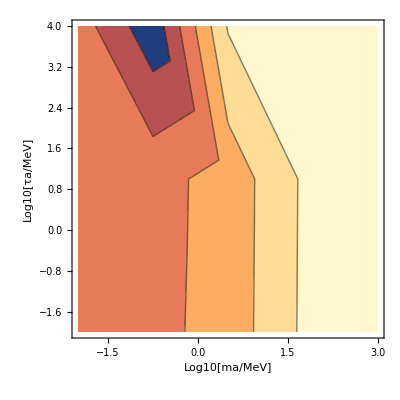

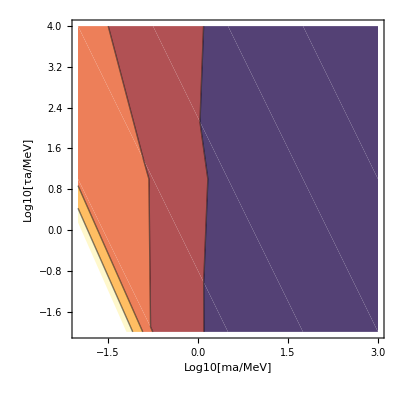

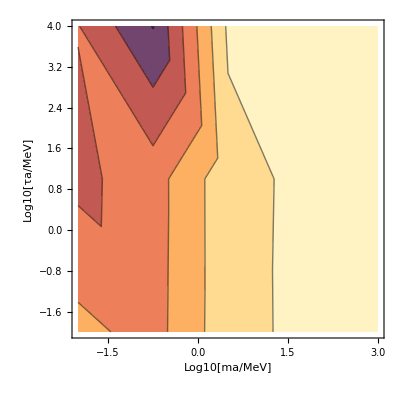

```mathematica
ListContourPlot[tab1[[All,{1,2,4}]],Contours->{2,2.25,2.5,2.75,3},FrameLabel->{"Log10[ma/MeV]","Log10[τa/MeV]","Neff, Treh = 10^3 GeV"}]

ListContourPlot[tab1[[All,{1,2,5}]],Contours->{0.23,0.24,0.25,0.26,0.27,0.28},FrameLabel->{"Log10[ma/MeV]","Log10[τa/MeV]","Yp, Treh = 10^3 GeV"}]

ListContourPlot[tab1[[All,{1,2,6}]],Contours->{1.2,1.4,1.6,1.8,2.0,2.2,2.4,2.6},FrameLabel->{"Log10[ma/MeV]","Log10[τa/MeV]","DH, Treh = 10^3 GeV"}]
```